```mathematica
d1=0.2;
d2=0.08;
mu=0.8;
cof=0.00125;   (*квадрат растояние hw*)
m=0.204;
T=0.0086;   (*100 K*)
eta=m/(√(d1^2+d2^2));
nu=(d1*d2)/(d1^2+d2^2);
```

```mathematica
a:=(2*Pi)/cof 2*d1*d2*(1-eta);
b:=(2*Pi)/cof*(mu^2-(√(d1^2+d2^2)-m)^2);
c:=(2*Pi^2*T*mu)/cof; 
{a,b,c,eta,nu}
```

{8.51759,3216.34,108.645,0.947046,0.344828}

```mathematica
En[n_]:=√(cof*n+(d1+d2-m)^2);
En[500]
```

0.794214

```mathematica
{(1-eta)^2,(eta*nu)^2/4}*(d1^2*d2^2)/(cof*mu)
{(1-eta)^2,(eta*nu)^2,(3*(eta*nu)^2)/a,2*eta*nu}(4*d1^2*d2^2)/(cof*mu*a)
```

{0.00071785,0.00682537}

{0.000337114,0.0128212,0.00451579,0.0785211}

```mathematica
g[x_]:= BesselJ[0,x];
g1[x_]:=√(2/(Pi*x))Cos[x-Pi/4];
{BesselJ[0,10.0],g1[10.0]}
```

{-0.245936,-0.246761}

```mathematica
A = (1-eta)^2+(eta^2*nu^2)/4;
B = 4/a*((1-eta)^2+eta^2*nu^2);
C1 =12/a^2 eta^2*nu^2; 
D1 = (8*eta*nu)/a;
tg = B/(4*A-C1);
{A, (4*A-C1)*√(1+tg^2), D1}
```

{0.0294657,0.112635,0.306723}

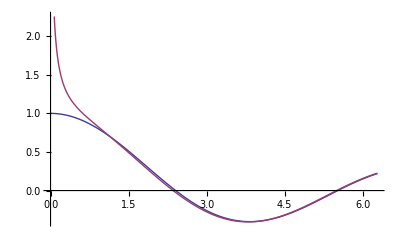

```mathematica
Plot[{BesselJ[0,x],g1[x]},{x,0,2Pi}]
```